# Multi-Way Tag Systems in Coordinatized Rulial Space

Dean Song Gladish

Carleton Class of 2020, mentor James Boyd @ WSS, 2022.

Abstract: To advance our understanding of computational irreducibility, my project will study the behavior of tag systems with different rules and initial conditions, as evaluated as singleway rules and multiway tag systems. My project focuses on comparisons of singleway and multiway behavior, exploring explosive, degenerate, and cyclic behavior, visualizing novel instances of the Ruliology. By generating analogues of Turing Machine Groups with multiway tag systems, the work provides a new coordinatized method for studying the Ruliad and Rulial space.

## Section 1. Functions & Dependencies.

To properly and clearly describe the evolution of the Post Tag System, we implement ideas within the Wolfram Language code. This section aims to describe ideas and arguments in a clear narrative format, explaining how Post’s tag system is studied and how the tag system becomes a Stag System in the Wolfram Language Code, using sections for each major step (function) or point of clarification/pivot.

### Subsection 1. Make Shifted Tag System with an Arbitrary Set of Rules

The idea is to look at tag systems as they evolve across time. What’s the best way to do that? With the implementation of Table with NestGraph, which permits the generation of graphs with layered digraph embedding, and portray the evolution of new tag systems in the Wolfram language code.

Plot the time evolution of an arbitrary binary tag system for time steps i = 1, 2, ..., n.

```mathematica
Table[NestGraph[ReplaceList[{
{left___,0,0,s___}:>{left,s,1,0,0},
{left___,1,0,s___}:>{left,s,0,1},
{left___,0,1,s___}:>{left,s,1,1,0},
{left___,1,1,s___}:>{left,s,0,1}}],{{1,1}},i,VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),GraphLayout->"LayeredDigraphEmbedding",PerformanceGoal->"Quality",ImageSize->Automatic],{i,1,8}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Take a closer look and plot the nth time step with definition of MultiwayTagSystem.

```mathematica
MultiwayTagSystem[rule_,init_,t_]:=NestGraph[
rule,
init,
t,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality",
ImageSize->Full
]
```

```mathematica
MultiwayTagSystem[ReplaceList[{
{left___,0,0,s___}:>{left,s,1,0,0},
{left___,1,0,s___}:>{left,s,0,1},
{left___,0,1,s___}:>{left,s,1,1,0},
{left___,1,1,s___}:>{left,s,0,1}}],
{{1,1}},
8
]
```

-Graphics-

Take a closer look and plot the first few complements of the MultiwayTagSystem vertex list, providing the length of the complement.

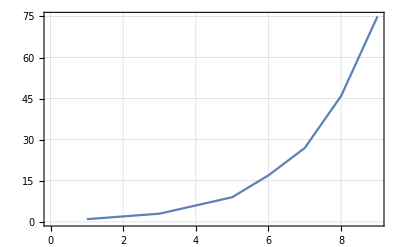

```mathematica
ListLinePlot[Table[
Length[

Complement[

VertexList[MultiwayTagSystem[ReplaceList[{
{left___,0,0,s___}:>{left,s,1,0,0},
{left___,1,0,s___}:>{left,s,0,1},
{left___,0,1,s___}:>{left,s,1,1,0},
{left___,1,1,s___}:>{left,s,0,1}}],
{{1,1}},
t
]],

VertexList[MultiwayTagSystem[ReplaceList[{
{left___,0,0,s___}:>{left,s,1,0,0},
{left___,1,0,s___}:>{left,s,0,1},
{left___,0,1,s___}:>{left,s,1,1,0},
{left___,1,1,s___}:>{left,s,0,1}}],
{{1,1}},
t-1
]]


]],{t,2,10}],PlotTheme->"Detailed",ImageSize->Automatic]
```

Take the greater complement from time step t - 1 to time step t, for the MultiwayTagSystem function.

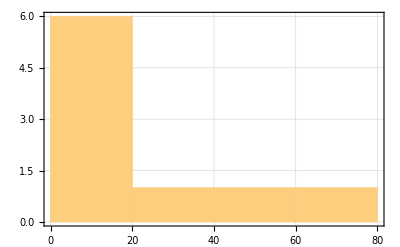

```mathematica
Histogram[Table[
Length[

Complement[

VertexList[MultiwayTagSystem[ReplaceList[{
{left___,0,0,s___}:>{left,s,1,0,0},
{left___,1,0,s___}:>{left,s,0,1},
{left___,0,1,s___}:>{left,s,1,1,0},
{left___,1,1,s___}:>{left,s,0,1}}],
{{1,1}},
t
]],

VertexList[MultiwayTagSystem[ReplaceList[{
{left___,0,0,s___}:>{left,s,1,0,0},
{left___,1,0,s___}:>{left,s,0,1},
{left___,0,1,s___}:>{left,s,1,1,0},
{left___,1,1,s___}:>{left,s,0,1}}],
{{1,1}},
t-1
]]


]],{t,2,10}],5,PlotTheme->"Detailed"]
```

Instantiate the idea: Random Multi-way Tag Systems based on visualizing tag system possibilities in the form of a multi-way graph.

```mathematica
RandomMultiwayTagSystem[g_]:=Table[ArrayPlot[Reverse@Transpose[PadRight[With[{vertices=VertexList[g],randomInit=Table[RandomInteger[{0,1},3],8]},Table[FindShortestPath[g,First[VertexList[g]],vertices[[i]]],{i,1,Length[vertices]}]][[i]],{Automatic,Automatic},.25]],Frame->True,ColorRules->{0->Hue[.95,.4,1.4],1->Hue[.1,.1,.1]},Mesh->True],{i,1,Length[VertexList[g]]}]
```

Repurpose the code for RandomPathCanyons, creating the random multi-way tag system from the beginning with the accompaniment of string templates.

```mathematica
Labeled[
NestGraph[ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,0,0,1}],
{left___,1,0,s___}:>Flatten[{left,s,0,0,1}],
{left___,0,1,s___}:>Flatten[{left,s,0,0,1}],
{left___,1,1,s___}:>Flatten[{left,s,0,0,1}]}],{{1,0,0}},4,VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),GraphLayout->"LayeredDigraphEmbedding",PerformanceGoal->"Quality",ImageSize->Full],
StringTemplate["{0,0,s___}->`a`
{1,0,s___}->`b`
{0,1,s___}->`c`
{1,1,s___}->`d`
`e`"][<|
"a"->{0,0,1},
"b"->{0,0,1},
"c":>{0,0,1},
"d":>{0,0,1},
"e":>{1,0,0}
|>]]
```

-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 0, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 0, 0}

The initial AllPathCanyons function, named because it finds the “generational” plots of binary tag systems.

```mathematica
AllPathCanyons[g_]:=Table[
ArrayPlot[
Reverse@Transpose[PadRight[
With[{vertices=VertexList[g]
,randomInit=Table[RandomInteger[{0,1},3],8]}
,Table[
FindShortestPath[g,First[VertexList[g]],vertices[[i]]],{i,1,Length[vertices]}
]][[i]]
,{Automatic,Automatic},.25]]
,Frame->True
,ColorRules->{0->Hue[.95,.4,1.4],1->Hue[.1,.1,.1]}
,Mesh->True
,ImageSize->Tiny
]
,{i,1,Length[VertexList[g]]}
]
```

The initial AllPathCanyons function, applied to the “stag” system (0, 0) -> (0, 0, 1), (1, 0) -> (0, 0, 1), (0, 1) -> (0, 0, 1), (1, 1) -> (0, 0, 1) with initial condition (1, 0, 0).

```mathematica
AllPathCanyons[
NestGraph[
ReplaceList[{
{left___,0,0,s___}:>{left,s,0,0,1},
{left___,1,0,s___}:>{left,s,0,0,1},
{left___,0,1,s___}:>{left,s,0,0,1},
{left___,1,1,s___}:>{left,s,0,0,1}}]
,{{1,0,0}}
,8
,VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&)
,GraphLayout->"LayeredDigraphEmbedding"
,PerformanceGoal->"Quality"
]
]
```

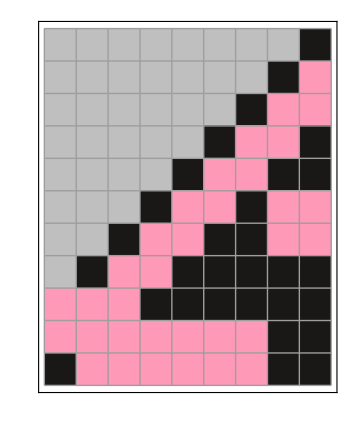
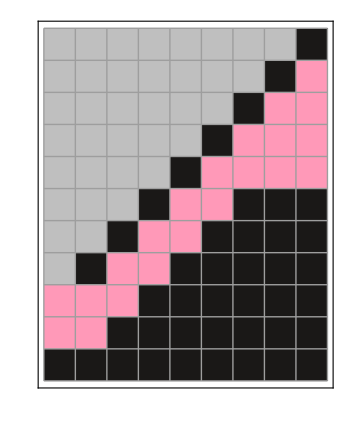
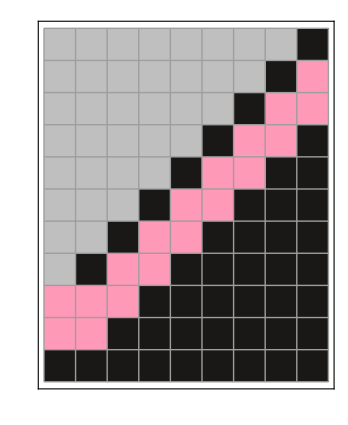

The Multi-Way NestGraph for {0,0,s___}->{1, 0, 0}, {1,0,s___}->{1, 0}, {0,1,s___}->{0, 0, 0}, {1,1,s___}->{0, 0}, with initial condition {0, 0, 0}.

```mathematica
Labeled[NestGraph[ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,Tuples[{0,1},3][[5]]}],
{left___,1,0,s___}:>Flatten[{left,s,Tuples[{0,1},2][[3]]}],
{left___,0,1,s___}:>Flatten[{left,s,Tuples[{0,1},3][[1]]}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},2][[1]]}]}],{Tuples[{0,1},3][[1]]},3,VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality",
ImageSize->Full],
StringTemplate["{0,0,s___}->`a`
{1,0,s___}->`b`
{0,1,s___}->`c`
{1,1,s___}->`d`
`e`"]
[<|
"a"->Tuples[{0,1},3][[5]],
"b"->Tuples[{0,1},2][[3]],
"c":>Tuples[{0,1},3][[1]],
"d":>Tuples[{0,1},2][[1]],
"e":>Tuples[{0,1},3][[1]]
|>]]
```

-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{1, 0}
{0,1,s___}->{0, 0, 0}
{1,1,s___}->{0, 0}
{0, 0, 0}

### Subsection 2. The Temperature Plots with GraphDistanceMatrix

The Temperature Plot for all Graph Distance Matrices.

```mathematica
Table[
Labeled[
ArrayPlot[GraphDistanceMatrix[{{"[◼]", "BranchialGraph"}}[NestGraph[ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i1]]}],
{left___,1,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i2]]}],
{left___,0,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i3]]}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i4]]}]}],
{Tuples[{0,1},l][[k]]},
t,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"]]]/.∞->0,
ColorFunction->"TemperatureMap"]
,
StringTemplate["{0,0,s___}->`a`
{1,0,s___}->`b`
{0,1,s___}->`c`
{1,1,s___}->`d`
`e`"]
[<|
"a"->Tuples[{0,1},j][[i1]],
"b"->Tuples[{0,1},j][[i2]],
"c":>Tuples[{0,1},j][[i3]],
"d":>Tuples[{0,1},j][[i4]],
"e":>Tuples[{0,1},l][[k]]
|>]]
,{t,1,5},
{i1,2^(j-1),2^(j-1)},
{i2,2^(j-1),2^(j-1)},
{i3,2^(j-1),2^(j-1)},
{i4,2^(j-1),2^(j-1)},
{j,3,3},
{k,2^l,2^l},
{l,3,3}]/.{{{{{{{x_}}}}}}}->x
```

The Temperature Plot for one Graph Distance Matrix instance.

```mathematica
g = {{"[◼]", "BranchialGraph"}}[NestGraph[ReplaceList[{
{left___,0,0,s___}:>{left,s,1,0,0},
{left___,1,0,s___}:>{left,s,0,1,1},
{left___,0,1,s___}:>{left,s,1,0,1},
{left___,1,1,s___}:>{left,s,1,1,1}
}],
{{1,1,0}},
5,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality",
ImageSize->Large]]
```

-Graphics-

The Graph Distance Matrix for one Graph Distance Matrix instance.

```mathematica
Style[MatrixForm[GraphDistanceMatrix[g]],12]
```

(0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 0 | 1 | 2 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 1 | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 2 | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 2 | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | 1 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | 1 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 2 | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | 1 | 2 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | 1 | 2 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | 1 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 2 | 1 | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 2 | 1 | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | 1 | 2 | 2 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | 1 | 2 | 2 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | 1 | 1 | 1 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 0 | 1 | 1 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 2 | 1 | 1 | 0 | 1 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 2 | 1 | 1 | 1 | 0 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 1 | 1 | 1 | 2 | 2 | 0)

The ArrayPlot for one Graph Distance Matrix instance, with labels.

```mathematica
Labeled[
ArrayPlot[GraphDistanceMatrix[g]/.∞->0,
ColorFunction->"TemperatureMap", 
PlotLegends->Automatic],
StringTemplate["{0,0,s___}->`a`
{1,0,s___}->`b`
{0,1,s___}->`c`
{1,1,s___}->`d`
`e`"]
[<|
"a"->{1,0,0},
"b"->{0,1,1},
"c":>{1,0,1},
"d":>{1,1,1},
"e":> {1,1,0}
|>]]
```

-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{1, 0, 1}
{1,1,s___}->{1, 1, 1}
{1, 1, 0}

## Section 2. Descriptions of the Functions

The AllPathCanyonsBinary function.

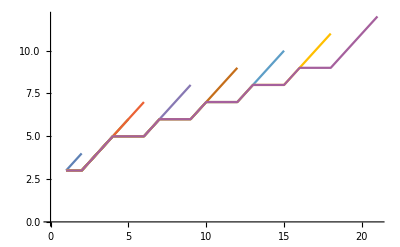
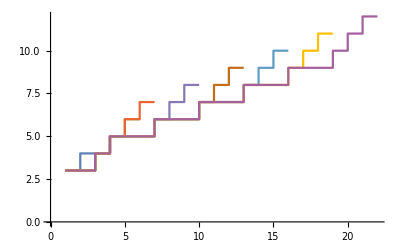
First, a brief description of the AllPathCanyonsBinary function; what this function does, is it takes a multi-way graph and then graphically displays this, much like our original multi-way tag systems plot with 0 and 1 as our constituents. The AllPathCanyonsBinary function is meant to take a NestGraph generated via our multi-way tag system rules. This NestGraph is generated based on a set of rules and an initial condition and then, provided the vertices of the given graph, revisits the FindPath function (or alternatively, the FindShortestPath function) on our graph such that we find the first & last element of the vertex list function all the way to Infinity, that allows us to find all paths. That is how we get our list of numbers; within the multi-way system we can portray tag system evolution via the AllPathCanyonsBinary function, that describes the lengths at all paths symbolically. 
-Graphics--Graphics-
These graphs represent the evolution of the tag system specified by

(0,0,s___) -> (0,1)

(1,0,s___)->(0,1,0)

(0,1,s___)->(1,0)

(1,1,s___)->(0,0,0)

(0,1,1)

```mathematica
The meaning of this is that as we time step from (1, 2, ..., n), we are plotting the length of the same tag system throughout n time steps with cyclic consequences. On the macro-level, the point is that we want to explore the relationship between multi-way and single-way behavior. The interaction between multi-way and single-way behavior is that we can visualize generational plots, named aptly because some of them are explosive, degenerate, and periodic. Some of these cycles depend on which path we take in the multi-way tag system. Because the function AllPathCanyons is designed to generate all tag systems at once, we can isolate single tag systems from the multi-way tag system graph, likewise we can isolate single tag systems from the ListStepPlot or ListLinePlots provided, therefore we can visualize black and pink squares that represent 1 and 0 respectively, and that show us the progression of a single-way tag system captured as a moment in the multi-way tag system graph as a single leaf vertex.
```

```mathematica
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
```

By bringing the ListStepPlot out of the nested tables we are able to plot them overlaid together, furthermore we are able to highlight all paths and shortest paths along the multi-way graph. We know that there are different single-way behaviors (explosive, degenerate, and periodic). Because the tag system above specifies a generally explosive single-way behavior across paths, visualizing explosive behavior in which the graph naturally tends to increment by a length of 1 but only when the conditions (1, 0) and (1, 1) are met somewhere in the string, since we can replace at any point in the string. Probably because our two-length tag system rules are manifesting cyclically, according to the three-length versus two-length tag system rules, we can specify tag systems that are explosive, or tag systems that are strictly incrementing.

(0, 0, s___) -> (1, 1)

(1, 0, s___) -> (1, 0, 0)

(0, 1, s___) -> (1, 0)

(1, 1, s___) -> (0, 1, 1)

(0, 0, 1)

The question is if any, what is the correspondence between single-way and multi-way behavior? The correspondence is that single-way behavior is manifested in each multi-way graph, if we follow the vertices.

## Section 3. Interesting Tag Systems

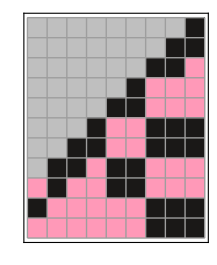
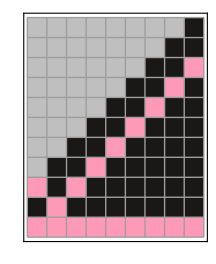
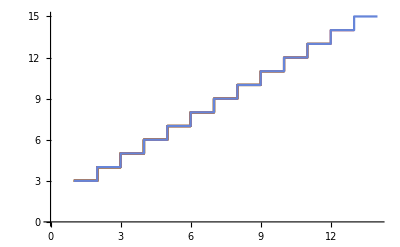
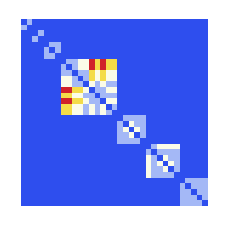
With regard to the implementation of the distance matrices, interesting is most nearly synonymous with the generation of cyclic behavior as seen on the graph distance matrix. Because our tag systems can be designed to create 4-cycles for instance, cycling through rules 1, 2, 3, and 4, we can generate interesting observed tag systems such as 

Tag System Example #1.
* (0,  0) -> (0, 0, 1), 
* (1, 0) -> (0, 1, 1), 
* (0, 1) -> (0, 1, 1), 
* (1, 1) -> (0, 1, 1)
* (0, 1, 0)
Leading to a checkerboard-like shape with accompanying ListLinePlot.
-Graphics--Graphics--Graphics-
The temperature maps for the graph distance matrix describes, along the diagonal, the identity matrix for which blue indicates a distance of 0. Whereas on the other hand, the graph distance matrix & branchial graph functions are colorizing the scale for 0, 1, 2, 3, and 4, for the sake of visualization infinity is oddly colored blue, for which blue describes infinite distance or alternatively 0, while values of 0 are ice cold and values of 4 are burning up. Let’s say we look at the 5th time step for the rules. 

It’s this tag system #1 which generates fractal-like tag system shapes which simply means that this tag system, selected for its resemblance to a chessboard, is one of the greatest tag systems of all time the reason being that the initial condition (0, 1, 0) leads to a layer of black color; 1s are being pushed further toward the top of the tag system which means that the (0, 0) -> (0, 0, 1) rule. The rules can be inserted at any location, right or left of the string allowing for untouched strings of (0, 0, 1) to be maintained, because in this single-way tag system 1s will simply pile up above (0, 0, 1). That is one of the most exciting relationships between single-way and multi-way behavior that has ever been seen, because even though we may not follow it all the way to the end of the branch, we definitely observe its pattern which occurs at ... 0, 0, .... 

Tag System Example #2. 
* (0, 0, s___) -> (1, 0)
* (1, 0, s___) -> (0, 1, 1)
* (0, 1, s___) -> (1, 1)
* (1, 1, s___) -> (0, 0, 0)
* (1, 1, 1)

-Graphics-
The values before the heat map are expressed in Matrix Form. 

(0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | 2 | 2 | 4 | 3 | 4 | 3 | 3 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | 2 | 2 | 4 | 3 | 4 | 3 | 3 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | 1 | 1 | 3 | 2 | 3 | 2 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 2 | 1 | 0 | 1 | 3 | 2 | 3 | 2 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 2 | 1 | 1 | 0 | 2 | 1 | 2 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 4 | 4 | 3 | 3 | 2 | 0 | 1 | 1 | 2 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 3 | 3 | 2 | 2 | 1 | 1 | 0 | 1 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 4 | 4 | 3 | 3 | 2 | 1 | 1 | 0 | 2 | 2 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 3 | 3 | 2 | 2 | 1 | 2 | 1 | 2 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 3 | 3 | 2 | 2 | 1 | 2 | 1 | 2 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 2 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 2 | 0 | 2 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 2 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 2 | 2 | 2 | 2 | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | 1 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 1 | 0 | 2 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 1 | 2 | 0 | 2 | 1 | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 1 | 1 | 2 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 2 | 1 | 1 | 1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | 1 | 1 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | 1 | 1 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 0 | 1 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 0 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | 1 | 1 | 0)

Are all single-way paths in a multi-way system similar in behavior? The stag system 
* (0, 0) -> (0, 1)
* (1, 0) -> (0, 1, 0)
* (0, 1) -> (1, 0)
* (1, 1) -> (0, 0, 0)
* (0, 1, 1)
makes differential single-way paths.

-Graphics--Graphics--Graphics-

Tag System Example #2. 
* (0,0,s___) -> (0, 1)
* (1,0,s___) -> (0, 1, 0)
* (0,1,s___ ) -> (1, 0)
* (1,1,s___) -> (0, 0, 0)
* (0, 1, 1)

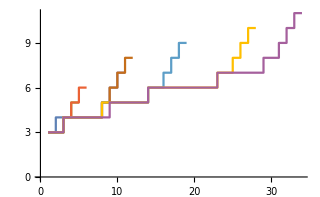
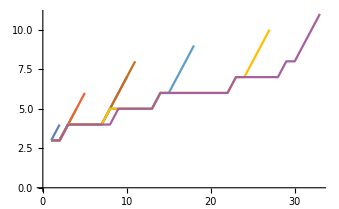

```mathematica
The ListStepPlot function, for which AllPathCanyonsBinary already records the length, has cyclic similarity in behavior in 4 steps.
```

Branchial graph for the tag system with 4-complete and 5-complete cycles.

```mathematica
{{"[◼]", "BranchialGraph"}}[NestGraph[
ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,0,0,0}],
{left___,1,0,s___}:>Flatten[{left,s,0,0,0}],
{left___,0,1,s___}:>Flatten[{left,s,1,1}],
{left___,1,1,s___}:>Flatten[{left,s,1,0,1}]
}],
{{1,1,1}},
5,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]]
```

-Graphics-

Multi-Way Graph for All Tag System Rules

```mathematica
Table[
Labeled[NestGraph[ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i1]]}],
{left___,1,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i2]]}],
{left___,0,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i3]]}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i4]]}]
}],
{Tuples[{0,1},l][[k]]},
t,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"],
StringTemplate["{0,0,s___}->`a`
{1,0,s___}->`b`
{0,1,s___}->`c`
{1,1,s___}->`d`
`e`"]
[<|
"a"->Tuples[{0,1},j][[i1]],
"b"->Tuples[{0,1},j][[i2]],
"c":>Tuples[{0,1},j][[i3]],
"d":>Tuples[{0,1},j][[i4]],
"e":>Tuples[{0,1},l][[k]]
|>]
],
{t,1,10},
{i1,2^j,2^j},
{i2,2^j,2^j},
{i3,2^j,2^j},
{i4,2^j,2^j},
{j,3,3},
{k,2^l,2^l},
{l,3,3}]/.{{{{{{{x_}}}}}}} -> x
```

{-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{1, 1, 1}
{0,1,s___}->{1, 1, 1}
{1,1,s___}->{1, 1, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{1, 1, 1}
{0,1,s___}->{1, 1, 1}
{1,1,s___}->{1, 1, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{1, 1, 1}
{0,1,s___}->{1, 1, 1}
{1,1,s___}->{1, 1, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{1, 1, 1}
{0,1,s___}->{1, 1, 1}
{1,1,s___}->{1, 1, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{1, 1, 1}
{0,1,s___}->{1, 1, 1}
{1,1,s___}->{1, 1, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{1, 1, 1}
{0,1,s___}->{1, 1, 1}
{1,1,s___}->{1, 1, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{1, 1, 1}
{0,1,s___}->{1, 1, 1}
{1,1,s___}->{1, 1, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{1, 1, 1}
{0,1,s___}->{1, 1, 1}
{1,1,s___}->{1, 1, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{1, 1, 1}
{0,1,s___}->{1, 1, 1}
{1,1,s___}->{1, 1, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{1, 1, 1}
{0,1,s___}->{1, 1, 1}
{1,1,s___}->{1, 1, 1}
{1, 1, 1}}

Tag System Example #3. 
* (0,0,s___) -> (0, 0, 1)
* (1,0,s___) -> (0, 0, 1)
* (0,1,s___ ) -> (0, 0, 1)
* (1,1,s___) -> (0, 0, 1)
* (1, 0, 0)

-Graphics-

## Compare behaviors of different paths

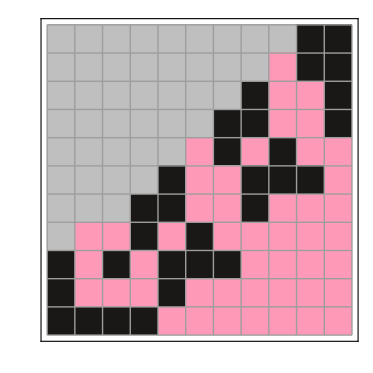
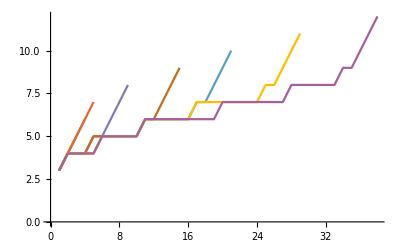
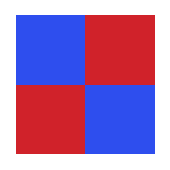
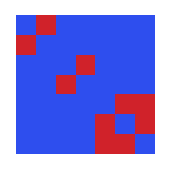
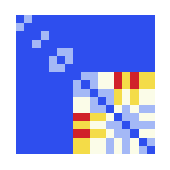
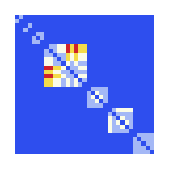
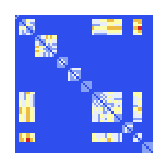
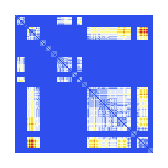
## Generation Plot Abiding by the rules * (left___,0,0,s___) -> (left, s, 1,0) * (left___,1,0,s___) -> (0,1,1) * (left___,0,1,s___) -> (1,1) * (left___,1,1,s___) ->{0,0,0) * (1,1,1) we can derive explosive and straight paths. There are many behaviors to consider, because it’s a multi-way system at 10 steps. Portraying the effect of rule length 2, which transfers (left___, 0, 0, s___) to (left, s, 1, 0) and (left___, 0, 1, s___) to (left, s, 1, 1), when the paths are exploding they create (0, 1, 0) and (0, 0, 0) while when the paths are maintaining the same length they create the patterns (1, 0) and (1, 1). Focus on the new idea for tag systems, for which they can pick up the rules from anywhere in the string. Distributed, interior tag systems, also known as stag systems, are not really tag systems! In order to get something to decay, the (1, 0) for instance has to be shortened; in the Post tag system one is chopping off three at the beginning and either getting two added or four added, and that’s why it’s the marginal case. In the Post tag system, one is chopping off three at the beginning and either getting two added or four added, and the tag system is always going to explode because the length is always getting bigger. -Graphics- ListLinePlot of Lengths With the same tag system rule (Tag System Example #2 with initial condition (0,1,0)), * (0, 0) -> (0, 1) * (1, 0) -> (0, 1, 0) * (0, 1) -> (1, 0) * (1, 1) -> (0, 0, 0) It’s possible to find the shortest length path in terms of path length. For instance, the block of code Length /@ FindShortestPath[g, First[VertexList[g]], VertexList[g][[Length[VertexList[g]]]]] allows us to find the length array of the given tag system; and if we ant to find a longer array, then increase the number of time steps, inclusive of the first step. The finding for this one is that having a tag system comprised of different lengths for the initial rules results in a linearly increasing shortest path, to delineate nothing regarding paths that are perhaps longer and still produce explosive behavior in that cyclically, in four-step for our particular example, exhibits an explosion when the current string can only be rewritten with expansive rules (that is rules which rewrite the string to a higher dimension) and stalls flatly when the current string can only be rewritten with diminishing rules, that is rules which map greater lengths to equal or lesser lengths. Question: For time steps 1,2, ..., n, what does the tag system rule * (0, 0) -> (0, 1) * (1, 0) -> (0, 1, 0) * (0, 1) -> (1, 0) * (1, 1) -> (0, 0, 0) * (0, 1, 0) look like in terms of our ListStepPlot function? -Graphics- State Transition Graphs GraphDistanceMatrix Array Plot Suppose we have the rule-set * (0, 0, s___) -> (1, 0) * (1, 0, s___) -> (0, 1, 1) * (0, 1, s___) -> (1, 1) * (1, 1, s___) -> (0, 0, 0) * (1, 1, 1) -Graphics--Graphics--Graphics--Graphics--Graphics--Graphics- Based on this example, it appears that the “tag system branches” are tangentially-related, the explosive nature of which is reflected in this graph. Let’s take a closer look. -Graphics- Depending on which branch you follow, your string might decrease in size or increase in size. Confluence Non-Cumulative Growth Rate (ListLinePlot and Histogram) (0, 0, s___) -> (1, 0) (1, 0, s___) -> (0, 1, 1) (0, 1, s___) -> (1, 1) (1, 1, s___) -> (0, 0, 0) (1, 1, 1) Multi-way behavior demonstrated does corroborate that varying length of the initial rules leads to explosive & periodic multi-way binary tag system re-writing. The only one of its kind? No. 111 1000 0011 001111 0111111 11111111 -Graphics- The observed behavior for this tag system could be that following the same sequence of multi-way steps allows patterns like -Graphics- patterns to keep repeating, because we are assigning (1, 1) to (0, 0, 0) and then assigning (1, 0) to (0, 1, 1) at any location in the string therefore the stag system allows us to visualize each reachable path which repeats on a small scale.

```mathematica
Branchial Graphs
```

Branchial graph for the tag system with 4-complete and 5-complete cycles.

```mathematica
g = NestGraph[ReplaceList[{
{left___,0,0,s___}:>{left,s,0,0,0},
{left___,1,0,s___}:>{left,s,0,1,0},
{left___,0,1,s___}:>{left,s,1,0},
{left___,1,1,s___}:>{left,s,1,1,1}
}],
{{1,0,1}},
6,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality",
ImageSize->Full
,VertexLabels->Thread[VertexList[g]->(Length[#]&/@VertexList[g])]
]

Labeled[g,
StringTemplate["{0,0,s___}->`a`
{1,0,s___}->`b`
{0,1,s___}->`c`
{1,1,s___}->`d`
`e`"]
[<|
"a"->{0,0,0},
"b"->{0,1,0},
"c":>{1,0},
"d":>{1,1,1},
"e":>{1,0,1}
|>]
]

HighlightGraph[g,Style[PathGraph[FindShortestPath[g,First[VertexList[g]],VertexList[g][[Length[VertexList[g]]]]],DirectedEdges->True],Red]]
```

-Graphics-

Tag System #6.

## Concluding remarks

To summarize in conclusion, providing future plans & ideas for extension of the work, it would be brilliant to engage in further explorations of interesting tag system behavior. Whereas if we are implementing the tag system with different lengths for the rules, such as 
(0,0)->(0,1), (1,0)->(0,1,0), (0,1)->(1,0), and (1,1)->(0,0,0), it appears that the greatest factor in generating explosive behavior is variability in the initial conditions’ length. Applying this same tag system rule to the initial NestGraph which is the basis for our ListStepPlot in that we are taking the length of each path in the multi-way NestGraph, the shortest path from the initial state to the end state is the one in which the initial condition (0, 1, 0) is essentially inverted by the tag system. 
-Graphics-
The evidence suggests that the confluence of systems is consistent across permutations of tag systems. The multi-computational behavior mentioned is most evident via the alteration of initial rules, which can across our four and eight initial rules tend toward the degenerate forms, which typically do not arise due to the nature of string rewriting.

## Keywords

Post Tag System

String Rewriting

Multi-Way & One-Way

## Acknowledgment

Props go to James for being such a kind mentor; and Stephen Wolfram defining the direction of this project toward methodically working upward. And to Post for providing the principal tag system.

## References

Mentor James Boyd, who teaches us keyboard shortcuts instead of Command + V. His passion (for entailment cones and) for multi-way computation in tag systems, and his insistence on having us meet with Nik, really kept things going.

Nik Murzin, whose generation of TwoWayMultiReplace has been nothing less than instrumental because he is the one who provides the scope and options for functions like TwoWayMultiReplace, with Identity, Uniquify, Canonicalize, and KeyMap Associations in .m nonetheless. Nik wrote things like Utilities, TwoWayRule, SubexpressionPositions, Rewriting, Quantifiers, MultiReplace, MultiCoReplace, MultiBiReplace, Metamathematics, Legacy, and Inference. He actually understands how the Mathematica kernel works!

Nik also does things like equational logic, axiomatic theory, and equation proof. When he is building the kernel, he builds things like Graph, LinkedHypergraph, Multicomputation, MulticomputationLoader, MulticomputationMain, MultiStringReplace, Utilities, and WFR. In fact, it is Nik who has created Tuples, HoldTuples, MatchSubstitutions. It’s so important for focusing on tag systems. It is Nik who has allowed the tag system rules to be applied anywhere in the current string.

Credit goes to Utkarsh for explaining how sequentality works so we didn’t think the past history had any bearing on the result of applying the tag system at any given time.